# Grid

## Setup

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Universita\MAGISTRALE\MasterThesis\Mathematica

```mathematica
Get["MyPackage.wl"]
```

```mathematica
alldata=Import["data.m"]
```

<|cellVal→{ν→0.3,Yp→2.5×10^9,ϵp→3.009×10^-11,ϵf→2.3895×10^-11,EBDp→303000000,EBDf→1.574×10^8,l0→1/40,w0→1,tp0→1/40000,tf0→1/100000,ξ0→3/1000,ϵ1max→0.05},tankVal→{d→5,Pt→50000,Vtank→1,Vftot→1,f→0.1},gasVal→{patm→101325,Tstd→288.15,γair→1.4,ρstdair→1.225,cv→717.2,cp→1.0042}|>

```mathematica
tmp={EBDp->236 10^6,EBDf->150 10^6,ϵp->3.9,ϵf->2.9,tp0->25 10^-6,tf0->2 10^-6};
```

```mathematica
(2 tp0 ϵf+tf0 ϵp)/(ϵf ϵp)Min[ϵp EBDp,ϵf EBDf]/.tmp
```

5876.92

```mathematica
(2 tp0)/ϵp Min[ϵp EBDp,ϵf EBDf]/.tmp
```

585.205

```mathematica
{tf0,tp0}/.celldata//N//ScientificForm
```

{1.×10^-5,2.5×10^-5}

```mathematica
(4 10^-11 2 10^-6+2ϵf tp0)/(4 10^-11 ϵf)/.celldata
```

1.3337×10^6

```mathematica
(2 tp0)/(4 10^-11)/.celldata
```

1250000

```mathematica
ϵf/.celldata
```

2.3895×10^-11

```mathematica
ϵp/.celldata
```

3.009×10^-11

```mathematica
25 10^-6==tp0/.celldata
```

True

```mathematica
celldata=alldata["cellVal"];
```

```mathematica
lenscell=Import["lenscell.m"];lenscell//Dataset
```

```mathematica
opts={GridLines->Automatic,GridLinesStyle->LightGray,LabelStyle->{Black,Bold,FontFamily->"Times New Roman",FontSize->12},AxesStyle->{FontFamily->"Times New Roman"},Frame->True};
```

```mathematica
NumDer[x_,y_]:=D[Interpolation[CombineVec[x,y]][h],h]/.h->x;
```

```mathematica
Delta[x_]:=x[[1]]-x
```

```mathematica
systemdata={d->5,Pt->100 10^3,T->10,zsub->4.7,Δhb->4,ρw->1000};
systemdata=Join[systemdata,{A->π d^2/4/.systemdata}]//N
```

{d→5.,Pt→100000.,T→10.,zsub→4.7,Δhb→4.,ρw→1000.,A→19.635}

## Model

```mathematica
halfcell=lenscell["nomgeom"];
cell=Join[{2 halfcell[[1]]},halfcell[[2;;4]]];
```

```mathematica
CC=lenscell["C"]
```

(w0 ϵf ϵp lc[h])/(2 tp0 ϵf+tf0 ϵp)

```mathematica
Funit[VV_]:=2lenscell["F"]/.V->VV;Funit[V]
```

-(V^2 w0 ϵf ϵp lc'[h])/(4 (2 tp0 ϵf+tf0 ϵp))

```mathematica
Trapz[cell[[1]],Funit[50000]/.tp0->0.167 10^-3/.celldata/.lc'[h]->NumDer[halfcell[[1]],halfcell[[2]]]]
```

{14.4695}

```mathematica
1/2 CC 50000^2/.tp0->0.167 10^-3/.celldata/.lc[h]->Max@cell[[2]]
```

14.4694

Cs = (NR-1)C,

hs = NR/2 4h =2 NR h

dCs/dhs=(NR-1)/(2 NR)dC/dh

```mathematica
Fs[V_,Nr_]:=(Nr-1)/Nr Funit[V]
```

```mathematica
hh=halfcell[[1]];
hcell=cell[[1]];
hu=2hcell;
```

```mathematica
ϵ=Pt T/.systemdata
```

1.×10^6

```mathematica
maxϵ=lenscell["Uelmax"]
```

14.4694

```mathematica
Nu=ϵ/maxϵ
```

69111.2

```mathematica
{hcmax=Max@hcell,hcmin=Min@hcell}
```

{0.02,0.0150207}

```mathematica
{zmax= 0.95Δhb/.systemdata,zmin=-zmax}
```

{3.8,-3.8}

```mathematica
NR=Nr/.Solve[Nr (hcmax-hcmin)/2==zmax ,Nr][[1]]/.systemdata//Ceiling
```

1527

```mathematica
NC=Nu/(2NR)//Ceiling
```

23

```mathematica
NN=NC 2NR
```

70242

```mathematica
Δhs1=NR Delta@hcell;
Δhs2=-NR Delta@hcell;
```

```mathematica
z1=(2 zmax)/(hcmin-hcmax)(hcell-hcmin)+zmax;
z2=(2 zmax)/(hcmax-hcmin)(hcell-hcmin)-zmax;
```

```mathematica
Fs1[V1_]:=NC Fs[VV1,NR]/.tp0->0.167 10^-3/.lc'[h]->NumDer[halfcell[[1]],halfcell[[2]]]/.celldata/.VV1->V1;
Fs2[V2_]:=NC Fs[VV2,NR]/.tp0->0.167 10^-3/.lc'[h]->NumDer[halfcell[[1]],halfcell[[2]]]/.celldata/.VV2->V2
```

```mathematica
FG[V1_,V2_]:=Fs1[V1]-Fs2[V2]
```

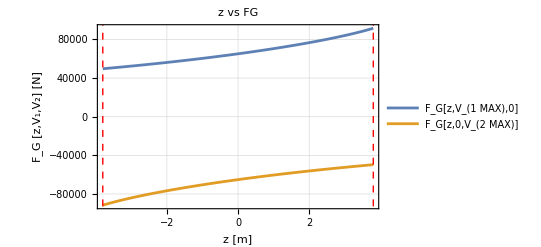

```mathematica
Block[{V1=50 10^3,V2=50 10^3},
Show[
ListPlot[{CombineVec[z1,FG[V1,0]],CombineVec[z2,FG[0,V2]]},
Joined->True,PlotLabel->"z vs FG",FrameLabel->{"z [m]","F_G [z,V_1,V_2] [N]"},Axes->False,Evaluate@opts,PlotLegends->AddLegend[{"F_G[z,V_(1  MAX),0]","F_G[z,0,V_(2  MAX)]"},Right,Center]],
XLine[zmax,{Thick,Red,Dashed}],XLine[zmin,{Thick,Red,Dashed}]
]
]
```

```mathematica
zFUel=Block[{V1=50 10^3,V2=50 10^3},Trapz[z1,FG[V1,0]]-Trapz[z2,FG[0,V2]]]
```

{1.01525×10^6}

```mathematica
NN maxϵ/zFUel
```

{1.00109}

### Export data

```mathematica
V1range=Range[0,50000,100];
V2range=Range[0,50000,100];
```

```mathematica
Fs1data=Table[Fs1[V1range[[i]]],{i,1,Length@V1range}];
Fs2data=Table[Fs2[V2range[[i]]],{i,1,Length@V2range}];
```

```mathematica
Export["..\\MATLAB\\Lens_cell\\Fs1data.xls",Fs1data]
Export["..\\MATLAB\\Lens_cell\\Fs2data.xls",Fs2data]
Export["..\\MATLAB\\Lens_cell\\V1data.xls",V1range]
Export["..\\MATLAB\\Lens_cell\\V2data.xls",V2range]
Export["..\\MATLAB\\Lens_cell\\z1data.xls",z1]
Export["..\\MATLAB\\Lens_cell\\z2data.xls",z2]
```

..\MATLAB\Lens_cell\Fs1data.xls

..\MATLAB\Lens_cell\Fs2data.xls

..\MATLAB\Lens_cell\V1data.xls

..\MATLAB\Lens_cell\V2data.xls

..\MATLAB\Lens_cell\z1data.xls

..\MATLAB\Lens_cell\z2data.xls